## Data

397_NO_REKT_1.txt

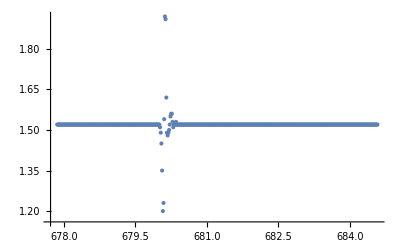

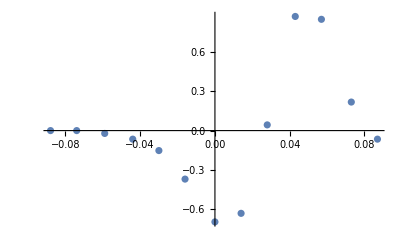

C:\Users\Lenovo\Documents\GitHub\electromotive-voltage\EV analysis\\inputData\cleaned_small_magnet\Cleaned_397_NO_REKT_1.txt

```mathematica
notePath = NotebookDirectory[];
filePath = "\\inputData\\small_magnet\\";
fileName = "397_NO_REKT_1.txt"
fullName = StringJoin[{notePath, filePath, fileName}];
data = Import[fullName, "Data"][[5;;-2]];
ListPlot[data]
heightShift = 3.3 / 1.52;
data = MapAt[heightShift# - 3.3&, data, {All,2}];

(*We'll shift the data so as to have the first minimum at t = 0.*)
positionOfMinimum = Position[data[[All, 2]], Min[data[[All, 2]]]][[1, 1]];
timeOfMinimum = data[[positionOfMinimum, 1]];

data = MapAt[# - timeOfMinimum &, data, {All, 1}];

(*We filter the data points whose voltage is outside an interval away from zero.*)
data = Select[data,-0.1<#[[1]] <0.1 &];

exportPath = StringJoin[{notePath, "\\inputData\\cleaned_small_magnet\\Cleaned_", fileName}];
dataPlot = ListPlot[data, PlotRange->All]
Export[exportPath, data, "CSV"]
```